```mathematica
SetDirectory[NotebookDirectory[]];
```

# Plot options for notebook

```mathematica
imgsize=400;
```

```mathematica
SetOptions[ListContourPlot,{PlotTheme->"Scientific",BaseStyle->{FontSize->30},ImageSize->imgsize}];
SetOptions[ListLinePlot,{PlotTheme->"Scientific",BaseStyle->{FontSize->18},ImageSize->imgsize}];
```

```mathematica
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/.Directive[x_,__]:>x);
```

```mathematica
colorFunc=("DefaultColorFunction"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListContourPlot]));
```

# Basis functions for the Galton-Watson process

Setup

### Pick range for nu

```mathematica
m=30;
```

```mathematica
nuMin=0.1//N;
nuMax=3.0//N;
```

```mathematica
deltanu=(nuMax-nuMin)/(m-1)//N;
```

```mathematica
nuGrid=Table[i,{i,nuMin,nuMax,(nuMax-nuMin)/(m-1)}]//N;
```

### Delta function approximation

```mathematica
sigma=0.01;
delta[x_,y_]:=Exp[-(x-y)^2/(2*sigma^2)]/Sqrt[2*Pi*sigma^2];
```

### Set Max time T and increment Delta t

```mathematica
tMax=1.0;
deltat=0.05;
nTime=IntegerPart[tMax/deltat];
```

```mathematica
tGrid=Table[i,{i,0,tMax,deltat}];
```

### Reaction rates

```mathematica
kB=0.5;
kD=1.5;
```

Algorithm helper functions

### Interpolate f

```mathematica
interpolate[f_]:=Module[
{fTable},
fTable=Table[{nuMin+i*deltanu,f[[i+1]]},{i,0,m-1}];
Return[Interpolation[fTable,InterpolationOrder->1]];
];
```

```mathematica
interpolateSmoothed[f_]:=Module[
{fSmoothed,fTable},
fSmoothed=LowpassFilter[f,0.5];
fTable=Table[{{nuMin+i*deltanu},fSmoothed[[i+1]]},{i,0,m-1}];
Return[Interpolation[fTable]];
];
```

### Solve the diff eqs

```mathematica
eps=0.01;
perturb[nu_,nuVary_]:=Exp[-(nu-nuVary)^2/(2*eps^2)]/Sqrt[2.0*Pi*eps^2];
fPerturb[fInterp_,nu_,nuVary_,mag_]:=fInterp[nu]+mag*perturb[nu,nuVary];
```

```mathematica
generateNuTrajectoryPerturb[fInterp_,nu0_,nuVary_,mag_]:=Module[
{sol,maxTime,nuSt,iMax}
,
sol=Quiet[NDSolve[{
nu'[t]==fPerturb[fInterp,nu[t],nuVary,mag],
nu[0]==nu0,
WhenEvent[nu[t]>=nuMax,"StopIntegration"],
WhenEvent[nu[t]<=nuMin,"StopIntegration"]},
nu,{t,0,tMax}]][[1]];
maxTime=(nu/.sol/.InterpolatingFunction[{a_},__]:>a)[[2]];
nuSt=Table[(nu/.sol)[tVal],{tVal,0,maxTime,deltat}];
Return[{nuSt,Length[nuSt]}]
];
```

```mathematica
generateNuTrajectory[fInterp_,nu0_]:=generateNuTrajectoryPerturb[fInterp,nu0,0.0,0.0];
```

```mathematica
solveDEs[fInterp_,nu0_]:=Module[
{numag,rtrue,nuTrajSt,nuLengthSt,nuLength,tbl,tblinterp,tblder,firstKey,correctLength,deleteList,nutrue,lengthTest}
,
numag=0.001;

(* Store r - first level = time, second = pos to vary *)
rtrue=Association[];

(* Go through all nu to vary at *)
Do[

(* Solve for nu trajectory for different perturbations *)
nuTrajSt=Association[];
nuLengthSt=Association[];
Do[
{nuTrajSt[nuVaryMag],nuLengthSt[nuVaryMag]}=generateNuTrajectoryPerturb[fInterp,nu0,nuVary,nuVaryMag];
,{nuVaryMag,-numag,numag,numag}];

(* Max length *)
nuLength=Min[Values[nuLengthSt]];

(* Go through all times *)
Do[
tbl=Table[{nuVaryMag,nuTrajSt[nuVaryMag][[iTime]]},{nuVaryMag,-numag,numag,numag}];
tblinterp=Interpolation[tbl,InterpolationOrder->2];
tblder=Derivative[1][tblinterp];
If[!KeyExistsQ[rtrue,iTime],rtrue[iTime]=Association[];];
rtrue[iTime][nuVary]=tblder[0.0];
,{iTime,1,nuLength}];

,{nuVary,nuGrid}];

(* Cut elements the max time of rtrue as necessary, such that all nuVary exist at each time *)
firstKey=Keys[rtrue][[1]];
correctLength=Length[rtrue[firstKey]];
deleteList={};
Do[
If[
Length[rtrue[key]]!=correctLength,
deleteList=Append[deleteList,key];
];
,{key,Keys[rtrue]}];
rtrue=KeyDrop[rtrue,deleteList];

(* Solve for the true nu *)
{nutrue,lengthTest}=generateNuTrajectory[fInterp,nu0];
nuLength=Min[Length[rtrue],lengthTest];

Return[{rtrue,nutrue,nuLength}];
];
```

#### Test

```mathematica
Clear[fInterp];
fInterp[nu_]:=Sin[nu];
{rsol,nusol,nuLength}=solveDEs[fInterp,1.0];
```

```mathematica
Manipulate[ListLinePlot[rsol[i],PlotRange->{0,2}],{i,1,Length[rsol],1}]
```

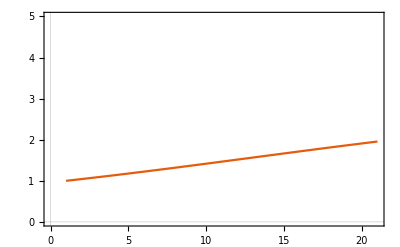

```mathematica
ListLinePlot[nusol,PlotRange->{0,5}]
```

### Average <n> from nu value

```mathematica
aveFromNu[nuTraj_]:=Table[1.0/(-1.0+Exp[nu]),{nu,nuTraj}];
```

### True average trajectory from the initial nu value

```mathematica
aveTrueFromNu0[nu0_,nTimeTraj_,deltat_]:=Module[
{aveTrue},
aveTrue=Association[];
aveTrue[0]=(1.0)/(-1.0+Exp[nu0]);
Do[
aveTrue[iTime]=aveTrue[iTime-1]+deltat*(kB-kD)*aveTrue[iTime-1];
,{iTime,1,nTimeTraj}];

Return[Values[aveTrue]]
];
```

### True solution

```mathematica
fTrue[nu_]:=(kD-kB)*(-Exp[-nu]+1);
```

### Solve true master equation prob dist

```mathematica
solveME[nmax_,nuIC_,krBirth_,krDeath_,nTimes_,dt_]:=Module[
{pSt}
,
(* Solution structure *)
pSt=Association[];
Do[
pSt[iTime]=Association[];
,{iTime,1,nTimes}];

(* IC *)
Do[
pSt[1][n]=fpt[n,nuIC];
,{n,0,nmax}];

(* Go *)
Do[
pSt[iTime][0]=pSt[iTime-1][0]+dt*krDeath*(pSt[iTime-1][1]);
Do[
pSt[iTime][n]=pSt[iTime-1][n]+dt*(krDeath*pSt[iTime-1][n+1]-krDeath*pSt[iTime-1][n]+krBirth*pSt[iTime-1][n-1]-krBirth*pSt[iTime-1][n]);
,{n,1,nmax-1}];
pSt[iTime][nmax]=pSt[iTime-1][nmax]+dt*(-krDeath*pSt[iTime-1][nmax]+krBirth*pSt[iTime-1][nmax-1]);
,{iTime,2,nTimes}];

Return[pSt];
];
```

### Boltz dist

```mathematica
fpt[n_,nu_]:=Exp[-(n+1)*nu]*(-1+Exp[nu]);
```

# Main algorithm v1: Integrate over IC in algorithm

Learning rate

```mathematica
nIter=200;
```

```mathematica
kLearningRate=0.02;
initialLearningRate=0.05;
finalLearningRate=0.01;
```

```mathematica
fMaxLearningRate[iter_]:=((finalLearningRate-initialLearningRate)/(Exp[-kLearningRate*(nIter-1)]-1))*(Exp[-kLearningRate(iter-1)]-1)+initialLearningRate;
```

```mathematica
fMaxLearningRate[iter_]:=initialLearningRate;
```

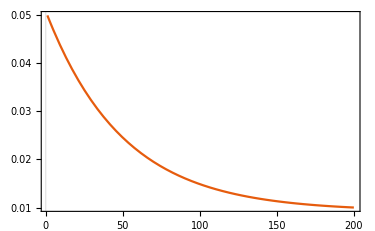

```mathematica
Plot[fMaxLearningRate[iter],{iter,1,nIter},PlotRange->{initialLearningRate,finalLearningRate}]
```

Run

```mathematica
nuGrid
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.}

```mathematica
inu0=16;
nu0=nuGrid[[inu0]]
```

1.6

```mathematica
(* Initialize F *)
(* Stored *)
(*f=f0;*)
(* True with noise *)
(*
noiseMag=0;
f=Table[fTrue[nuVal],{nuVal,nuGrid}]+RandomReal[noiseMag*{-1,1},m];
*)
(* Constant *)
f=ConstantArray[0.0,m];
(* Sin function *)
(*f=Table[Sin[nu],{nu,nuGrid}];*)

(* Store f *)
fSt=Association[];
fSt[0]=f;

Monitor[
Do[
(* Interpolate f *)
(*fInterp=interpolateSmoothed[f];*)
fInterp=interpolate[f];

(* Objective func update *)
dsdf=ConstantArray[0,m];

(* Generate nu trajectory, solve pdes *)
(* Also get the number of steps before this traj runs off the domain *)
{rTraj,nuTraj,nTimeTraj}=solveDEs[fInterp,nu0];

(* Generate the trajectory of the average from nu *)
aveTraj=aveFromNu[nuTraj];

(* Generate the true average trajectory from the initial nu0Eval *)
aveTrajTrue=aveTrueFromNu0[nu0,nTimeTraj,deltat];

(* Evaluate the objective function - table of nu to vary at *)
aveTrueSt={};
aveSt={};
varSt={};
varModSt={};
Do[
dsdf+=deltat*(aveTrajTrue[[iTime]]-aveTraj[[iTime]])*Values[rTraj[iTime]]*Table[Exp[-(nuv-nuTraj[[iTime]])^2/(2*0.01)],{nuv,nuGrid}];
AppendTo[aveTrueSt,aveTrajTrue[[iTime]]];
AppendTo[aveSt,aveTraj[[iTime]]];
AppendTo[varSt,Values[rTraj[iTime]][[inu0]]];
AppendTo[varModSt,Values[rTraj[iTime]][[inu0]]*Exp[-(nuGrid[[inu0]]-nuTraj[[iTime]])^2/(2*0.01)]];
,{iTime,1,nTimeTraj}];

(* Adjust magnitude such that the max is the learning rate *)
dsdf*=fMaxLearningRate[iIter]/Max[Abs[dsdf]];

(* Update the basis functions *)
f=Table[fInterp[nuVal],{nuVal,nuGrid}]-dsdf;

(* Store f *)
fSt[iIter]=f;

(* Plot *)
pltmax=1.5;
pltx={nuMin,nuMax};
plt=Show[
ListLinePlot[Transpose[{nuGrid,f}],PlotRange->{pltx,{0,pltmax}},AxesLabel->{"ν","F(ν)"},PlotStyle->{colors[[2]]}],
ListLinePlot[Transpose[{nuGrid,fSt[0]}],PlotRange->{pltx,{0,pltmax}},PlotStyle->{colors[[2]],Dashed}],
ListLinePlot[Table[{nuVal,fTrue[nuVal]},{nuVal,nuGrid}],PlotStyle->{colors[[1]],Dashed},PlotRange->{pltx,{0,pltmax}}]
,ImageSize->300
];

pltave=ListLinePlot[{aveTrueSt,aveSt},ImageSize->300];
pltvar=ListLinePlot[{varSt,varModSt},PlotRange->All,ImageSize->300];

,{iIter,1,nIter}];
,
GraphicsRow[{
ProgressIndicator[iIter,{1,nIter}]
,
plt
,
pltave
,
pltvar
}]
]
```

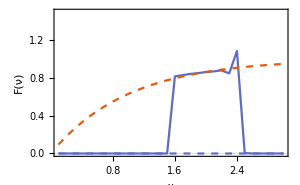

```mathematica
plt
```